Описание задачи
функция: t_i(x_i,c_i) = t_i^0(1 + 0.15* [x_i/c_i]^4)   i = OverBar[1 ,n], t_i^0 > 0
оптимизационная задача верхнего уровня:  min_c∑_(i=1)^n t_(i (x_i,c_i))x_i 
ограничения: на c: ∑_(i=1)^n c_i< C, c_i≥ 0
оптимизационная задача нижнего уровня: x_i = arg min_x∑_(i=1)^n ∫_0^x_i t_i(u,c_i)ⅆu
ограничения: на x: ∑_(i=1)^n x_i= F, x_i≥ 0
C > 0, F > 0
Задание: разработать эволюционный алгоритм, решающий задачу двухуровневой оптимизации для разных наборов значений
C > 0, F > 0,  n и   t_i^0 > 0,  i = OverBar[1 ,n]

```mathematica
(* Исходные данные *)
n = 3; m =50;С = 100; F = 100; t0 = 1; iterrationAmount = 500; w1 = 0.1; r = 2;
μ = 3; λ = 2; p = 2; crossoverProbability = 0.5; mutationProbability = 0.1;
w = 0.5; c1 = 0.3; c2 = 0.2;
variableNumberC = n;
variableNumberX = n;
populationNumberUpLevel = m;
populationNumberLowLevel = m;
currentIterration =1;
searchSpaceC = {0.01,С};
searchSpaceX = {0,F};
variablesVectorC = {};
variablesVectorX = {};
 quadraticApproximationKoef = ((n+1)*(n+1))/2 +n;
givenMSE = Max[{Total@Abs[searchSpaceC],Total@Abs[searchSpaceX]}]*0.3;
bestValue = {};
bestPosition= {};
bestParticlesValue = {};
bestParticlesPosition = {};

upperLevelFunctionValueListMin = {};
upperLevelFunctionValueListMax={};
lowerLevelFunctionValueListMin ={};
lowerLevelFunctionValueListMax ={};
upperLevelFunctionValueParticlesMin = {};
upperLevelFunctionValueParticlesMax = {};
```

```mathematica
(* 1. Инициализация *)
variablesVectorC = {};
If[n>1,
Table[{
variablesVectorC0 ={};
distributionVector = {};
For[i = n, i > 0, i --,
If[i > 0,
distributionVector = Append[
distributionVector,RandomReal[{0.001,1}]
]
]
];
distributionVector = Sort@distributionVector;
numbersWithoutOne =С*(RandomReal[{0,#}]&/@((distributionVector⟦#⟧-distributionVector⟦#-1⟧)&@Range[2,n]));
variablesVectorC0  = Append [
numbersWithoutOne, RandomReal[{0,С -Total@numbersWithoutOne}]
];
variablesVectorC  = Append[variablesVectorC ,variablesVectorC0
]
;},
m
],
Table[
{
variablesVectorC  =Append[
variablesVectorC , {RandomReal[{0,С}]}
]
},
m
]
];
variablesVectorX = {};
upperLevelFunctionValue ={};
If[n>1,
{
k = 1,
Table[
i=1;
variablesVectorX0 = {};
variablesVectorXWithoutOne = {};
upperLevelFunctionValue0 = {};
While[i<n,
variablesVectorXWithoutOne= Append[variablesVectorXWithoutOne,
(Values@(Minimize[{t0*(1+0.15*(x/variablesVectorC ⟦k,i⟧)^4), x≥0},x]⟦2⟧))⟦1⟧
];
upperLevelFunctionValue0 = Append [upperLevelFunctionValue0 ,
Minimize[{t0*(1+0.15*(x/variablesVectorC ⟦k,i⟧)^4), x≥0},x]⟦1⟧
];
i++
];
LastXValue = F - Total@variablesVectorXWithoutOne;
variablesVectorX0 = Append[variablesVectorXWithoutOne, LastXValue];
variablesVectorX = Append[variablesVectorX,variablesVectorX0 ];
upperLevelFunctionValue = Append[upperLevelFunctionValue,
Total[Flatten[{upperLevelFunctionValue0 ,t0*(1+0.15*(LastXValue/variablesVectorC ⟦k,i⟧)^4)}]]
];
k++,
m]
},
variablesVectorX = Table[Append[variablesVectorX ,F],m]
];

bestParticlesValue = upperLevelFunctionValue;
bestParticlesPosition = variablesVectorC;

parentsDataset =AssociationThread[Table[i,{i,m}]-> Table[AssociationThread[{"Tag","UpperVariables","LowerVariables","UpperLevelFunctionValue", "LowerLevelFunctionValue", "BestParticlesValue", "BestParticlesPosition", "Velocity"}->  {Table[1,m]⟦i⟧,variablesVectorC ⟦i⟧,variablesVectorX ⟦i⟧,upperLevelFunctionValue⟦i⟧,Table[1000000,m]⟦i⟧,upperLevelFunctionValue⟦i⟧,variablesVectorC ⟦i⟧, Table[Table[0, n],m]⟦i⟧}],{i,1,m}]]//Dataset
parentsDatasetKeysList = parentsDataset@Keys
variablesVectorC

bestUpperLevelMember =Keys[Select[(Transpose@parentsDataset )["UpperLevelFunctionValue"],#==Min@(Transpose@parentsDataset )["UpperLevelFunctionValue"]&]]
bestValue = parentsDataset[bestUpperLevelMember[1]]["BestParticlesValue"]
lowerValueForBestUp = parentsDataset[bestUpperLevelMember[1]]["LowerLevelFunctionValue"]
bestPosition= {};
For[i = 1, i<= n, i++,
bestPosition=Append[bestPosition, parentsDataset[bestUpperLevelMember[1]]["BestParticlesPosition"][i]]
]
bestPosition
```

{{0.242903,17.8815,11.6969},{3.27287,9.23954,27.9586},{12.2207,3.71904,69.5784},{8.78165,1.13103,49.8465},{16.7158,15.0818,38.4171},{0.825104,19.7578,73.6088},{1.44673,37.6911,54.5474},{27.026,0.195508,66.3839},{21.8423,6.62223,50.8479},{0.241326,4.73455,61.2084},{1.6961,7.74872,25.3456},{7.16105,4.95043,83.9577},{0.41565,8.04555,1.7276},{1.58334,39.0307,13.09},{2.12856,13.847,65.3465},{57.0439,0.47117,3.77959},{13.1677,7.99142,53.4731},{2.51864,28.9352,35.1466},{30.3787,30.127,31.6348},{1.88319,1.08961,65.4554},{2.06691,4.00711,15.1276},{24.1515,7.05421,13.1416},{8.96846,45.3553,2.76033},{6.8875,0.442245,59.6483},{23.7474,30.7674,42.5303},{6.84625,0.0023316,34.6435},{4.30334,5.45869,62.4949},{11.5928,0.0891258,57.7528},{14.3126,13.0341,63.9916},{16.2832,33.1404,9.2829},{4.55286,6.52735,48.5714},{4.39801,9.75701,58.5439},{15.3506,7.14166,7.04752},{2.81081,1.10299,42.5334},{0.512603,1.97235,55.3113},{66.9476,10.1195,21.9243},{6.17811,1.54106,66.9718},{3.23324,7.6911,86.9919},{19.0032,2.62633,55.9683},{15.9267,13.541,42.6342},{0.885894,11.1382,53.722},{3.52644,0.188551,94.4196},{4.017,4.17368,14.6834},{6.90325,1.56521,71.7478},{49.2682,7.20841,0.766134},{6.86629,0.525215,55.0294},{38.8538,0.910411,48.2086},{2.28122,40.5286,31.6815},{0.558596,2.71074,58.8763},{2.55699,11.2916,74.9728}}

3.18873

1000000

{3.52644,0.188551,94.4196}

```mathematica
iterrationCounter = 1;

Timing[
While[iterrationCounter ≤ iterrationAmount,

parentsDatasetKeysList = parentsDataset@Keys;
upperLevelVariablesVector =Table [ (Values@((Transpose@parentsDataset)["UpperVariables"]))⟦i⟧, {i,1,Length@(Values@((Transpose@parentsDataset)["UpperVariables"]))}];
lowerLevelVariablesVector = Table [ (Values@((Transpose@parentsDataset)["LowerVariables"]))⟦i⟧, {i,1,Length@(Values@((Transpose@parentsDataset)["LowerVariables"]))}];
keysOfTaggedVariables =Keys[Select[(Transpose@parentsDataset)["Tag"],#==1&]];
(* 2. Выбор родителей верхнего уровня *)
If [Length@keysOfTaggedVariables > 1,(* что с уловием, если переменных с тегом меньше !! *)
{taggedParentsDataset =KeyTake[parentsDataset,keysOfTaggedVariables];

bestUpperLevelMember =Keys[Select[(Transpose@taggedParentsDataset)["UpperLevelFunctionValue"],#==Min@(Transpose@taggedParentsDataset)["UpperLevelFunctionValue"]&]];
(*For[i=1,i≤ Length@bestUpperLevelMember,i++,
parentsDatasetKeysList = Delete[parentsDatasetKeysList,bestUpperLevelMember⟦i,1⟧]
];*)
keysForTournament = RandomSample[parentsDatasetKeysList,2*(μ-1)];
bestKeysFromTournament =TakeSmallest[(Transpose@KeyTake[parentsDataset,keysForTournament])["UpperLevelFunctionValue"],2];

chosenParentsVector = Append[Keys@bestKeysFromTournament,bestUpperLevelMember[1]];
}
];

(* 3. Оптимизация на верхнем уровне алгоритмом PSO *)
offspringVelocity = Table[0,Length@chosenParentsVector,n];
For[i = 1, i<= Length@chosenParentsVector, i++,
For[j = 1, j<= n, j++,
offspringVelocity⟦i,j⟧ = w * parentsDataset[chosenParentsVector[i]]["Velocity"][j] + c1 * RandomReal[] * (parentsDataset[chosenParentsVector[i]]["BestParticlesPosition"][j] - parentsDataset[chosenParentsVector[i]]["UpperVariables"][j]) + 
c2* RandomReal[] * (bestPosition⟦j⟧- parentsDataset[chosenParentsVector[i]]["UpperVariables"][j]) + RandomReal[{-2,2}]
]
]; 
upperOffspringVector =  Table[0,Length@chosenParentsVector,n];

For[i = 1, i<= Length@chosenParentsVector, i++,
For[j = 1, j<= n, j++,
newPos =parentsDataset[chosenParentsVector[i]]["UpperVariables"][j] + offspringVelocity⟦i,j⟧;
If[newPos < 0,
newPos = 0.001
];
upperOffspringVector⟦i,j⟧ = newPos
]
] ;

For[i = 1, i<= Length@chosenParentsVector, i++,
sum = Total@upperOffspringVector⟦i⟧;
If[sum > C,
{
dif = sum - C,
upperOffspringVector⟦i⟧ = upperOffspringVector⟦i⟧ - upperOffspringVector⟦i⟧/ sum * dif
}
]
];
lowerOffspringVector = {};
(* 4. Квадратичная аппроксимация *)
quadraticApproximationIndicator = 0;
quadraticProgrammingIndicator = 0;
evolutionaryOptimizationIndicator = 0;
If[ Length@keysOfTaggedVariables≥ quadraticApproximationKoef ,
{
upperLevelVariablesForApproximation = ( taggedParentsDataset[#]["UpperVariables"])&/@keysOfTaggedVariables;
lowerLevelVariablesForApproximation= ( taggedParentsDataset[#]["LowerVariables"])&/@keysOfTaggedVariables;
polynom = {};
For[
k = 1, k≤ n,k++,
yValues = {};
xValues ={};
polynom0 = {};
For[
l= 1, l≤ Length@taggedParentsDataset,l++,
yValues = Append[yValues,lowerLevelVariablesForApproximation[l,k]];
xValues = Append[xValues,upperLevelVariablesForApproximation[l,k]];
];
data = {xValues,yValues};
polynom0 = NonlinearModelFit[Transpose@data , a0+b0*x+c0*(x^2),{a0,b0,c0}, x];
polynom = Append[polynom,polynom0];
];
quadraticApproximationIndicator = 1;
}
];
If[quadraticApproximationIndicator == 1,
approximationError =polynom⟦#⟧["ANOVATableMeanSquares"]⟦2⟧&/@Range[Length@polynom];,
approximationError = {0};
];

(* 5. Оптимальное решение на нижнем уровне *)
(* 5.1. При удачной квадратичной аппроксимации *)
(* 5.1.1. Поиск значений переменных на нижнем уровне *)
If[
Select[approximationError,#>0&&#<givenMSE&
]≠{0},
{
parametrsValueMatrix = ( Values@polynom ⟦#,1,2⟧)&/@Range[Length@polynom];
For[
l = 1, l≤ Length@upperOffspringVector, l++,
lowerOffspringVector0 = {};
For[
k = 1, k≤ n, k++,
a = parametrsValueMatrix⟦k,1⟧;
b = parametrsValueMatrix⟦k,2⟧;
c = parametrsValueMatrix⟦k,3⟧;
lowerOffspringVector0 = Append[lowerOffspringVector0,
a + b*upperOffspringVector⟦l,k⟧+c*(upperOffspringVector⟦l,k⟧)^2]
];
sumOfLowerOffspringVector = Total@lowerOffspringVector0;
If[sumOfLowerOffspringVector  ≠ С ,
If[sumOfLowerOffspringVector  < С,
 {
missingSum = С - sumOfLowerOffspringVector,
For[ k= 1, k≤ n, k++,
lowerOffspringVector0 ⟦k⟧ = lowerOffspringVector0⟦k⟧ +  lowerOffspringVector0⟦k⟧/sumOfLowerOffspringVector*missingSum 
]
},
{
overwhelmingSum=  sumOfLowerOffspringVector - С,
For[ k= 1, k≤ n, k++,
lowerOffspringVector0 ⟦k⟧ = lowerOffspringVector0⟦k⟧ -  lowerOffspringVector0⟦k⟧/sumOfLowerOffspringVector*overwhelmingSum ]
}
]
];
lowerOffspringVector = Append[lowerOffspringVector,lowerOffspringVector0];
]
}
];

(* 5.1.2. Замена особей в популяции *)
If[quadraticApproximationIndicator == 1,
{
chosenMembersOfParentPopulation = RandomSample[Keys@parentsDataset,r];
upperVarForLowerLevelTournament = upperOffspringVector;
Table[upperVarForLowerLevelTournament =
 Append[upperVarForLowerLevelTournament,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["UpperVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
Table[offspringVelocity =
 Append[offspringVelocity ,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["Velocity"][#]&/@(Range[1,n])
],
{k,1,λ}
];
lowerVarForLowerLevelTournament = lowerOffspringVector;
Table[lowerVarForLowerLevelTournament =
 Append[lowerVarForLowerLevelTournament ,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["LowerVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
pool =Transpose@{Flatten@lowerVarForLowerLevelTournament,Flatten@upperVarForLowerLevelTournament};

lowerLevelFunctionValue =Total/@(Partition[(Integrate[t0*(1 + 0.15*(x/#⟦2⟧)^4),{x, 0 ,#⟦1⟧}]&/@pool ),n]);

pool1 = Partition[Flatten@Transpose@pool,n];
lowerLevelFunctionValue0 =lowerLevelFunctionValue;
positionOfBestOffspring  ={};
While[Length@positionOfBestOffspring < λ,
positionOfBestOffspring =Append [
positionOfBestOffspring ,Position[lowerLevelFunctionValue,Min@lowerLevelFunctionValue0]
];
lowerLevelFunctionValue0= DeleteCases[lowerLevelFunctionValue0, Min@lowerLevelFunctionValue0]
];
positionOfBestOffspring = Flatten@positionOfBestOffspring;
upperLevelFunctionValue={};
For[k=1,k≤ λ,k++,
upperLevelFunctionValue0 ={};
For[f = 1, f≤ n, f++,
upperLevelFunctionValue00 = t0*(1+0.15*(pool1⟦positionOfBestOffspring⟦k⟧⟧⟦f⟧/pool1⟦4+positionOfBestOffspring⟦k⟧⟧⟦f⟧)^4);
upperLevelFunctionValue0 =Append[upperLevelFunctionValue0,upperLevelFunctionValue00];
 ];
upperLevelFunctionValue =Append [upperLevelFunctionValue,Total@upperLevelFunctionValue0]
];

bestOffspringValue = {};
bestOffspringPosition = {};

For[ i = 1, i<=  λ,i++,
If[parentsDataset[chosenMembersOfParentPopulation⟦i⟧]["BestParticlesValue"]>= upperLevelFunctionValue⟦i⟧,
{bestOffspringValue = Append[bestOffspringValue ,upperLevelFunctionValue⟦i⟧];
bestOffspringPosition  = Append[bestOffspringPosition , pool1⟦5+positionOfBestOffspring⟦i⟧⟧]},
{bestOffspringValue = Append[bestOffspringValue ,parentsDataset[chosenMembersOfParentPopulation⟦i⟧]["BestParticlesValue"]];
bestOffspringPosition0={};
For[j = 1, j<= n, j++,
bestOffspringPosition0=Append[bestOffspringPosition0,parentsDataset[chosenMembersOfParentPopulation⟦i⟧]["BestParticlesPosition"][j]
]
];
bestOffspringPosition  = Append[bestOffspringPosition ,bestOffspringPosition0]
}
]
];

For[k=1,k≤ λ,k++,
parentsDataset =Insert[parentsDataset,
chosenMembersOfParentPopulation⟦k⟧->Association[
"Tag"-> 1,
"UpperVariables"->  pool1⟦5+positionOfBestOffspring⟦k⟧⟧,
"LowerVariables"-> pool1⟦positionOfBestOffspring⟦k⟧⟧,
"UpperLevelFunctionValue" ->upperLevelFunctionValue⟦k⟧,
"LowerLevelFunctionValue" -> lowerLevelFunctionValue⟦positionOfBestOffspring⟦k⟧⟧,
"BestParticlesValue" ->bestOffspringValue⟦k⟧,
"BestParticlesPosition" ->bestOffspringPosition⟦k⟧,
"Velocity" ->  offspringVelocity⟦positionOfBestOffspring⟦k⟧⟧
],
Key[chosenMembersOfParentPopulation⟦k⟧]
]
];
offspringVelocity = Delete[offspringVelocity,{{-1},{-2}}]
},
quadraticProgrammingIndicator = 1;
];

(* 5.3. Эволюционная оптимизация нижнего уровня *)
evolutionaryOptimizationIndicator =1;
quadraticProgrammingIndicator =1;
If[quadraticProgrammingIndicator == 1&& evolutionaryOptimizationIndicator ==1,
{
lowerLevelMembersAmountForEvOp= 3;,
lowerLevelMembersListForEvOp = {};,
For[i = 1, i≤ lowerLevelMembersAmountForEvOp, i++,
koef0 = RandomReal[{},n];
koef1 = Total@koef0;
lowerLevelMembersListForEvOp = Append[lowerLevelMembersListForEvOp,
100*koef0/koef1]
];
lowerLevelParentsVectorForEvFromDatasetKeys = RandomSample[Keys@parentsDataset,μ];
lowerLevelParentsVectorForEvFromDataset =Table[(parentsDataset[RandomSample[Keys@parentsDataset,2μ]⟦i⟧]["LowerVariables"][#]&/@Range[n]),{i,μ}];

(* 5.3.1. Кроссовер *)
g = Mean[lowerLevelParentsVectorForEvFromDataset ];
d = lowerLevelParentsVectorForEvFromDataset ⟦1⟧ - g;
If[d≠ 0,
w2 = variableNumberC /Abs[lowerLevelParentsVectorForEvFromDataset⟦1⟧ - g],
w2 = 0.1
];
w2 = 0.1;
lowerLevelOffspringVector= {};
For [i = 1, i≤ Length@chosenParentsVector, i++,
crossoverNumber = RandomReal[{0,1}];
If[crossoverNumber ≤   crossoverProbability,
{
crossoverOperator = lowerLevelParentsVectorForEvFromDataset⟦1⟧  +w1 *d + w2*((lowerLevelParentsVectorForEvFromDataset⟦3⟧-lowerLevelParentsVectorForEvFromDataset⟦2⟧)/2),
crossoverOperator=crossoverOperator*100/Total@crossoverOperator,
lowerLevelOffspringVector= Append[lowerLevelOffspringVector,crossoverOperator]
},
lowerLevelOffspringVector= Append[lowerLevelOffspringVector, RandomChoice[lowerLevelParentsVectorForEvFromDataset]]
]
];

(* 5.3.2. Полиномиальная мутация *)
 For[i = 1, i≤ Length@chosenParentsVector,i++,
polynomialMutationNumber = RandomReal[{0,1}];
If[polynomialMutationNumber ≤   mutationProbability,
{r1= RandomReal[{0,1}],
η = RandomReal[{0.1,100}],
If[r1≤ 0.5,
δ =(2*r1)^((1/η)+1),
δ = 1 -(2* (1-r1))^((1/η)+1)
],
lowerLevelOffspringVector⟦i⟧ =lowerLevelOffspringVector⟦i⟧+(lowerLevelParentsVectorForEvFromDataset⟦1⟧  - lowerLevelParentsVectorForEvFromDataset ⟦2⟧)*δ
}
]
]

}
];
(* 5.3.3. Замена особей в популяции *)
chosenMembersOfParentPopulation = RandomSample[Keys@parentsDataset,r];
upperVarForLowerLevelTournament = upperOffspringVector;
Table[upperVarForLowerLevelTournament =
 Append[upperVarForLowerLevelTournament,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["UpperVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
Table[offspringVelocity =
 Append[offspringVelocity ,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["Velocity"][#]&/@(Range[1,n])
],
{k,1,λ}
];
lowerVarForLowerLevelTournament = lowerLevelOffspringVector;
Table[lowerVarForLowerLevelTournament =
 Append[lowerVarForLowerLevelTournament ,
(parentsDataset[#]&/@chosenMembersOfParentPopulation)[k]["LowerVariables"][#]&/@(Range[1,n])
],
{k,1,λ}
];
pool =Transpose@{Flatten@lowerVarForLowerLevelTournament,Flatten@upperVarForLowerLevelTournament};
lowerLevelFunctionValue =Total/@(Partition[(Integrate[t0*(1 + 0.15*(x/#⟦2⟧)^4),{x, 0 ,#⟦1⟧}]&/@pool ),n]);
pool1 = Partition[Flatten@Transpose@pool,n];
lowerLevelFunctionValue0 =lowerLevelFunctionValue;
positionOfBestOffspring  ={};
While[Length@positionOfBestOffspring < λ,
positionOfBestOffspring =Append [
positionOfBestOffspring ,Position[lowerLevelFunctionValue,Min@lowerLevelFunctionValue0]
];
lowerLevelFunctionValue0= DeleteCases[lowerLevelFunctionValue0, Min@lowerLevelFunctionValue0]
];
positionOfBestOffspring = Flatten@positionOfBestOffspring;
upperLevelFunctionValue={};
For[k=1,k≤ λ,k++,
upperLevelFunctionValue0 ={};
For[f = 1, f≤ n, f++,
upperLevelFunctionValue00 = t0*(1+0.15*(pool1⟦positionOfBestOffspring⟦k⟧⟧⟦f⟧/pool1⟦4+positionOfBestOffspring⟦k⟧⟧⟦f⟧)^4);
upperLevelFunctionValue0 =Append[upperLevelFunctionValue0,upperLevelFunctionValue00];
 ];
upperLevelFunctionValue =Append [upperLevelFunctionValue,Total@upperLevelFunctionValue0]
];

bestOffspringValue = {};
bestOffspringPosition = {};

For[ i = 1, i<=  λ,i++,
If[parentsDataset[chosenMembersOfParentPopulation⟦i⟧]["BestParticlesValue"]>= upperLevelFunctionValue⟦i⟧,
{bestOffspringValue = Append[bestOffspringValue ,upperLevelFunctionValue⟦i⟧];
bestOffspringPosition  = Append[bestOffspringPosition , pool1⟦5+positionOfBestOffspring⟦i⟧⟧]},
{bestOffspringValue = Append[bestOffspringValue ,parentsDataset[chosenMembersOfParentPopulation⟦i⟧]["BestParticlesValue"]];
bestOffspringPosition0={};
For[j = 1, j<= n, j++,
bestOffspringPosition0=Append[bestOffspringPosition0,parentsDataset[chosenMembersOfParentPopulation⟦i⟧]["BestParticlesPosition"][j]]
];
bestOffspringPosition  = Append[bestOffspringPosition ,bestOffspringPosition0]
}
]
];

For[k=1,k≤ λ,k++,
parentsDataset =Insert[parentsDataset,
chosenMembersOfParentPopulation⟦k⟧->Association[
"Tag"-> 1,
"UpperVariables"->  pool1⟦5+positionOfBestOffspring⟦k⟧⟧,
"LowerVariables"-> pool1⟦positionOfBestOffspring⟦k⟧⟧,
"UpperLevelFunctionValue" ->upperLevelFunctionValue⟦k⟧,
"LowerLevelFunctionValue" -> lowerLevelFunctionValue⟦positionOfBestOffspring⟦k⟧⟧,
"BestParticlesValue" ->bestOffspringValue⟦k⟧,
"BestParticlesPosition" ->bestOffspringPosition⟦k⟧,
"Velocity" ->  offspringVelocity⟦positionOfBestOffspring⟦k⟧⟧
],
Key[chosenMembersOfParentPopulation⟦k⟧]
]
];

iterrationCounter++;
Print@iterrationCounter; 
upperLevelFunctionValueListMin = Append[upperLevelFunctionValueListMin ,Min@(parentsDataset[#]["UpperLevelFunctionValue"]&/@Range[1, m])];
upperLevelFunctionValueListMax= Append[upperLevelFunctionValueListMax,Max@(parentsDataset[#]["UpperLevelFunctionValue"]&/@Range[1, m])];
lowerLevelFunctionValueListMin = Append[lowerLevelFunctionValueListMin ,Min@(parentsDataset[#]["LowerLevelFunctionValue"]&/@Range[1, m])];
lowerLevelFunctionValueListMax= Append[lowerLevelFunctionValueListMax,Max@(parentsDataset[#]["LowerLevelFunctionValue"]&/@Range[1, m])];
upperLevelFunctionValueParticlesMin =  Append[upperLevelFunctionValueParticlesMin ,Min@(parentsDataset[#]["BestParticlesValue"]&/@Range[1, m])];
upperLevelFunctionValueParticlesMax = Append[upperLevelFunctionValueParticlesMax,Max@(parentsDataset[#]["BestParticlesValue"]&/@Range[1, m])];
]
]
```

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

241

242

243

244

245

246

247

248

249

250

251

252

253

254

255

256

257

258

259

260

261

262

263

264

265

266

267

268

269

270

271

272

273

274

275

276

277

278

279

280

281

282

283

284

285

286

287

288

289

290

291

292

293

294

295

296

297

298

299

300

301

302

303

304

305

306

307

308

309

310

311

312

313

314

315

316

317

318

319

320

321

322

323

324

325

326

327

328

329

330

331

332

333

334

335

336

337

338

339

340

341

342

343

344

345

346

347

348

349

350

351

352

353

354

355

356

357

358

359

360

361

362

363

364

365

366

367

368

369

370

371

372

373

374

375

376

377

378

379

380

381

382

383

384

385

386

387

388

389

390

391

392

393

394

395

396

397

398

399

400

401

402

403

404

405

406

407

408

409

410

411

412

413

414

415

416

417

418

419

420

421

422

423

424

425

426

427

428

429

430

431

432

433

434

435

436

437

438

439

440

441

442

443

444

445

446

447

448

449

450

451

452

453

454

455

456

457

458

459

460

461

462

463

464

465

466

467

468

469

470

471

472

473

474

475

476

477

478

479

480

481

482

483

484

485

486

487

488

489

490

491

492

493

494

495

496

497

498

499

500

501

{523.655,Null}

```mathematica
parentsDataset
```

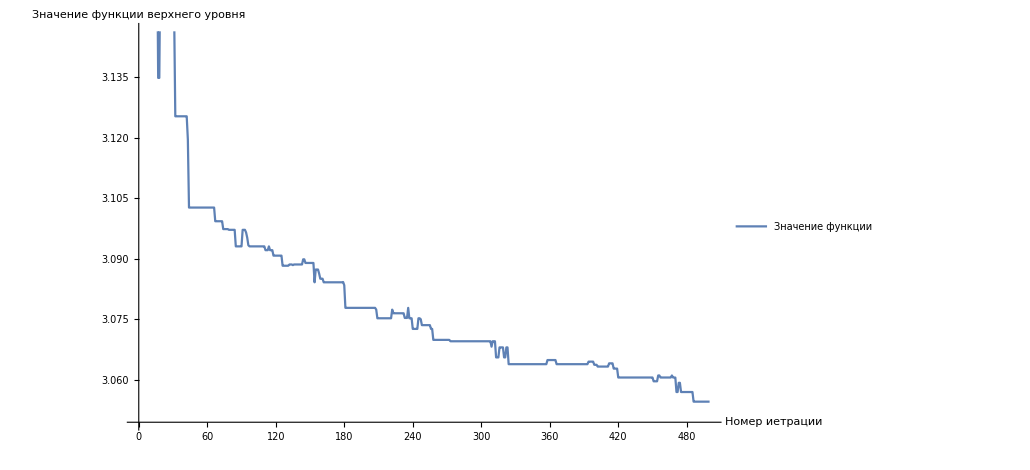

```mathematica
ListLinePlot[{upperLevelFunctionValueListMin}, AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{ "Значение функции"}]
```

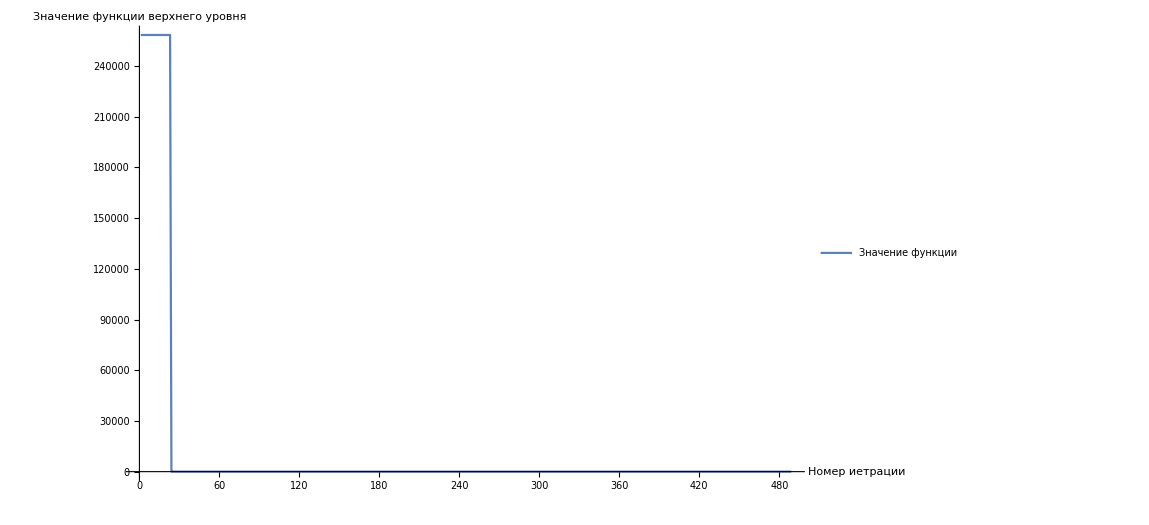

```mathematica
ListLinePlot[upperLevelFunctionValueListMax⟦12;;⟧, AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{ "Значение функции"}]
```

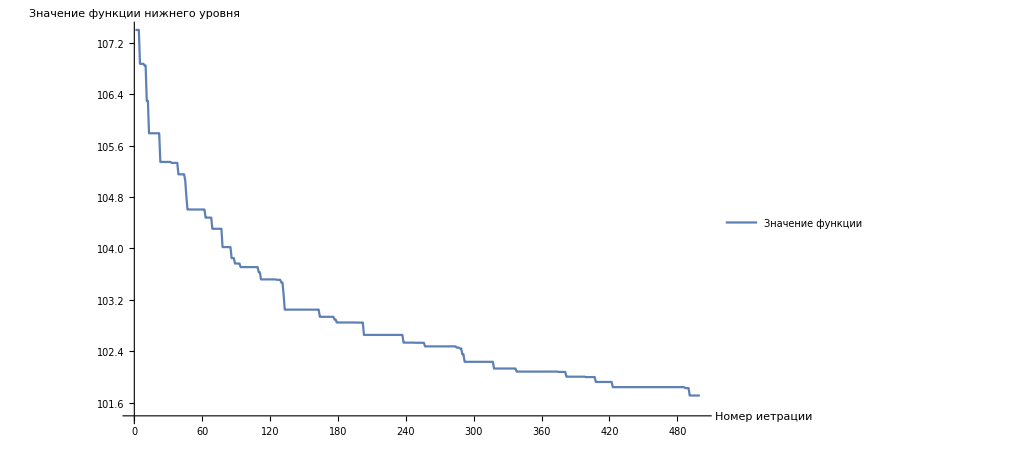

```mathematica
ListLinePlot[lowerLevelFunctionValueListMin,  AxesLabel->{"Номер иетрации", "Значение функции нижнего уровня"},PlotLegends->{ "Значение функции"} ]
```

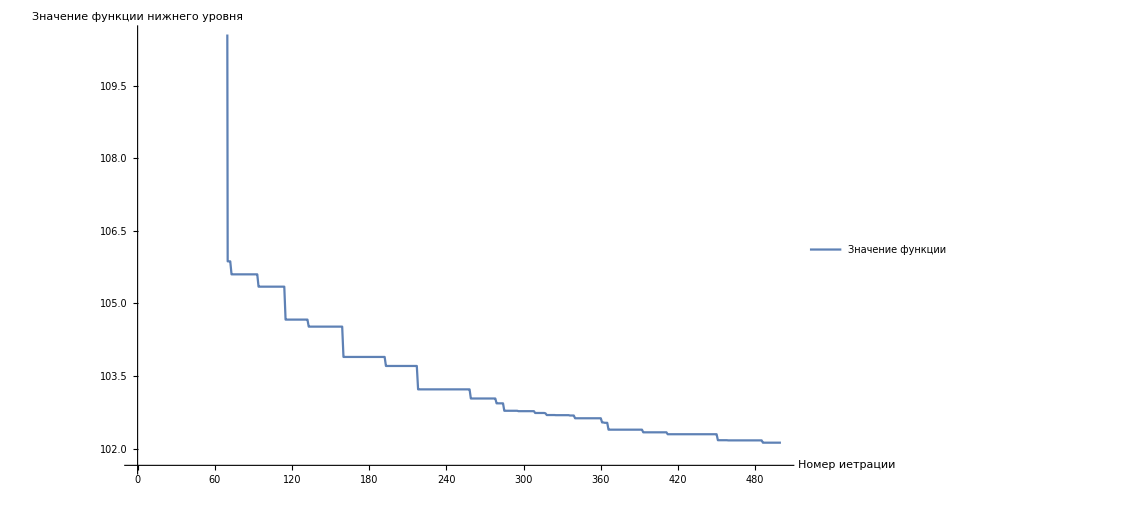

```mathematica
ListLinePlot[lowerLevelFunctionValueListMax, AxesLabel->{"Номер иетрации", "Значение функции нижнего уровня"},PlotLegends->{ "Значение функции"}]
```

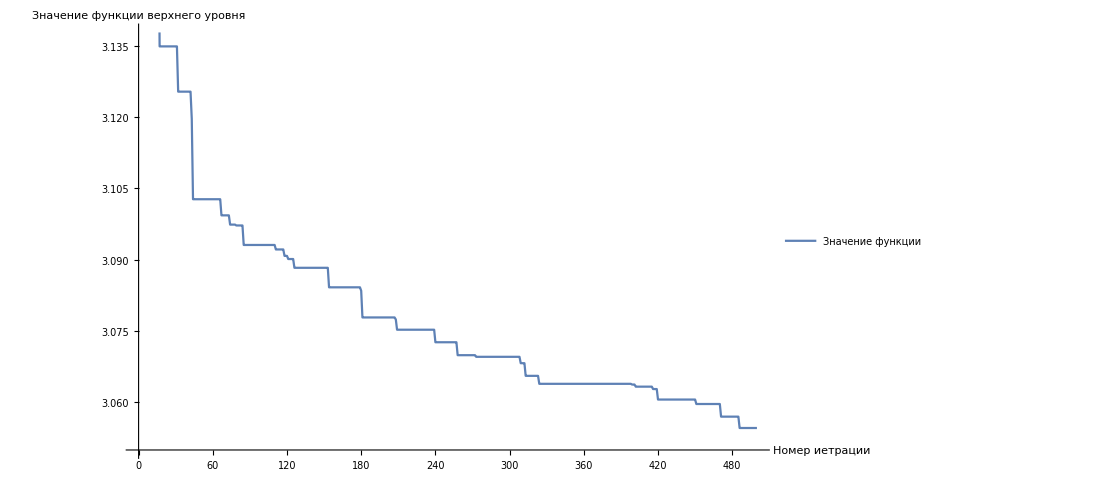

```mathematica
ListLinePlot[upperLevelFunctionValueParticlesMin , AxesLabel->{"Номер иетрации", "Значение функции верхнего уровня"},PlotLegends->{ "Значение функции"}]
```

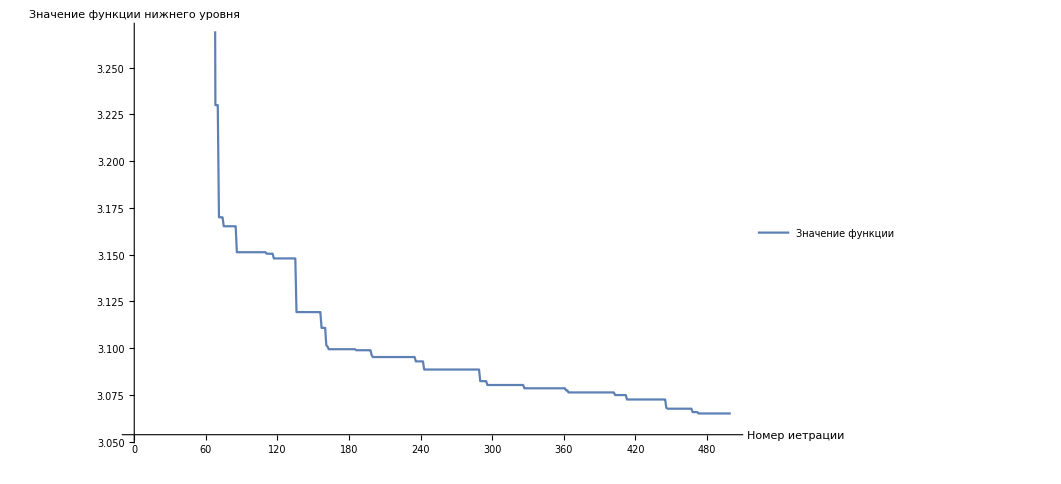

```mathematica
ListLinePlot[upperLevelFunctionValueParticlesMax, AxesLabel->{"Номер иетрации", "Значение функции нижнего уровня"},PlotLegends->{ "Значение функции"}]
```

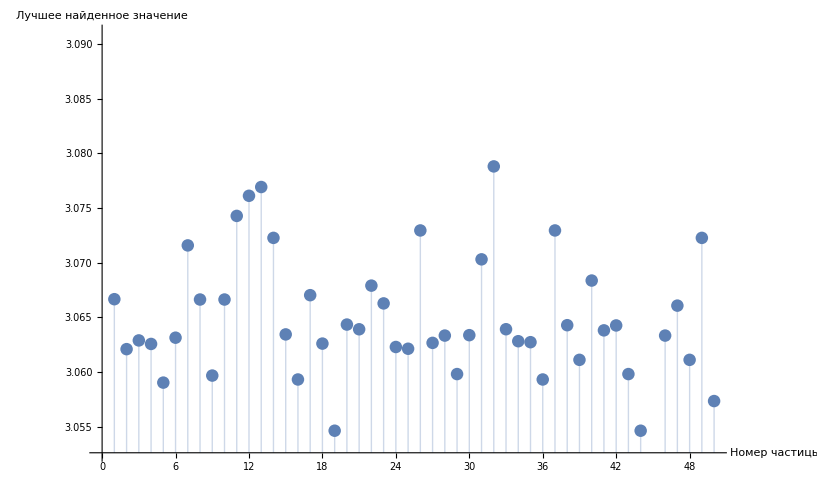

```mathematica
ListPlot[{parentsDataset[#]["UpperLevelFunctionValue"]&/@Range[Length@parentsDataset]},Filling->Axis, AxesLabel->{"Номер частицы", "Лучшее найденное значение"}]
```

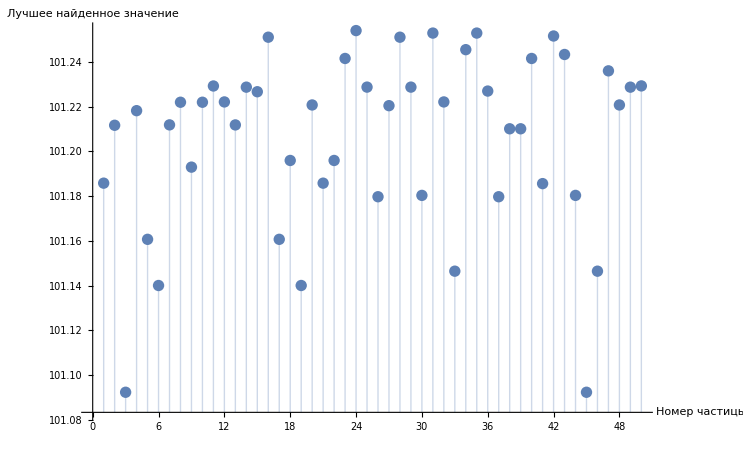

```mathematica
ListPlot[parentsDataset[#]["LowerLevelFunctionValue"]&/@Range[Length@parentsDataset],Filling->Axis, AxesLabel->{"Номер частицы", "Лучшее найденное значение"}]
```

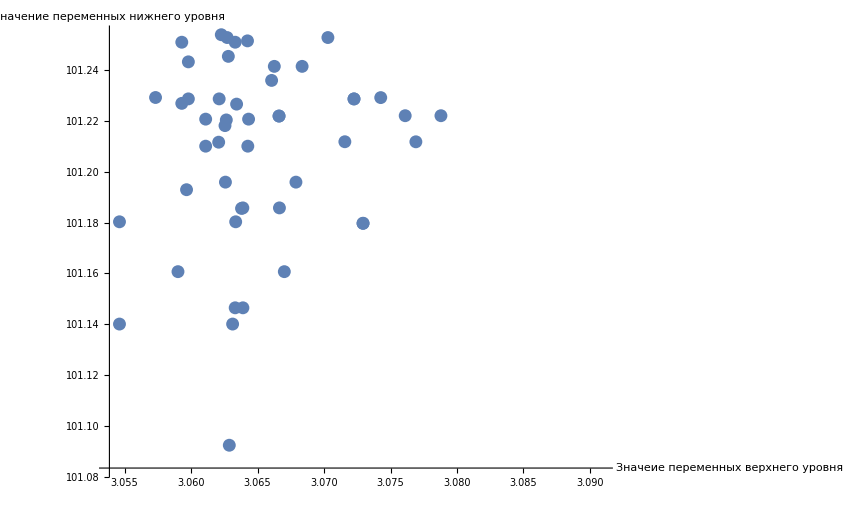

```mathematica
ListPlot[Transpose@{parentsDataset[#]["UpperLevelFunctionValue"]&/@Range[Length@parentsDataset],parentsDataset[#]["LowerLevelFunctionValue"]&/@Range[Length@parentsDataset]}, AxesLabel->{"Значеие переменных верхнего уровня", "Значение переменных нижнего уровня"}]
```